```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### WD parameters

```mathematica
WD=Import["/Users/NewUser/Documents/Qballs/WD.csv"];
WDrad=Import["/Users/NewUser/Documents/Qballs/WDradius.csv"];
WDreverse=Reverse/@WD;
Massreverse=Interpolation[WDreverse];
WDplot=Interpolation[WD];Radplot=Interpolation[WDrad];
```

```mathematica
Clear[vesc]
vesc[M_]:=Convert[Sqrt[GravitationalConstant*M/Radplot[M]*SolarMass/SolarRadius] 1/SpeedOfLight,d]
trigger[ρ_]:=If[ρ>10^8,10^-5*(ρ/(5*10^9))^(-1/2),1/(10000 √2)*(ρ/10^8)^-2]
triggermass=Interpolation[Table[{WDplot[logρ],trigger[10^logρ]},{logρ,5,10.6,0.01}]];
nionMeV[M_]:=Convert[10^Massreverse[M] Gram/Centimeter^3*SpeedOfLight^2/(12Giga ElectronVolt)*(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]*1/(Mega ElectronVolt)^3
nionMeV2[logρ_]:=3.7397260789901873*^-10 10^logρ
eboom[M_]:=Log10[10^-3((Integrate[4 Pi^2/15 T^3,{T,0,1}]+Integrate[Pi^(4/3)/3^(1/3)(Z nion)^(2/3)T,{T,0,1}]+Integrate[nion,{T,0,1}])(4 Pi/3(triggermass[M](200 *10^-13)^-1)^3)/.{Ef->(3 Pi^2 Z nion)^(1/3)}/.{nion->nionMeV[M],Z->6})]
param={ρdm->0.4 GeV/cm^3*(0.2GeV*10^-13 cm)^3,mdm->GeV 10^logmdm,v->10^-3,vesc->vesc[M],ρwd->nionMeV[M] MeV^3 12GeV (GeV/(10^3 MeV))^3,nion->nionMeV[1.25] MeV^3(GeV/(10^3 MeV))^3,mc->12GeV,Mpl->10^19 GeV,τwd->5 10^9 yr *(Pi 10^7 s/yr)(3 10^10 cm/s)(0.2GeV 10^-13 cm)^-1,Rwd->Radplot[M]sradius (7 10^10 cm/sradius) (0.2GeV 10^-13 cm)^-1,T->10^-6 GeV,σ->10^logσ cm^2}/.M->1.25;
```

#### DM Capture, efficient

```mathematica
Γtrans=FullSimplify[(ρdm/mdm π Rwd^2 vesc^2/v)/.param,{GeV>0}];
Rth=FullSimplify[((T Mpl^2)/(mdm (nion mc)))^(1/2)*0.2GeV 10^-13 cm/.param,GeV>0];
vth=FullSimplify[Sqrt[T/mdm]/.param];
Ncrit=FullSimplify[ρwd Rth^3/mdm/.param,GeV>0];
Nsg=FullSimplify[Max[2,(nion mc((T Mpl^2)/(mdm (nion mc)))^(3/2))/(10^logmdm GeV)/.param],GeV>0];
Msg=FullSimplify[Nsg mdm/.param,GeV>0];
Neq=( (Γtrans Rth^3)/(σ vth)(0.2 GeV 10^-13 cm)^-1)^(1/2)/.param;
Nlife=FullSimplify[Γtrans τwd/.param];
Rbh=FullSimplify[(Nsg 10^logmdm GeV)/((10^19 GeV)^2)(0.2 GeV 10^-13 cm)^1/.param,GeV>0];
Rdeg=FullSimplify[((10^19 GeV)^2)/((10^logmdm GeV)^3 Nsg^(1/3))(0.2 GeV 10^-13 cm),GeV>0];
```

```mathematica
Ntrigaccum=FullSimplify[(Min[Neq,Nlife]/Rth^3)^2 σ vth(triggermass[1.25] cm)^3(10^-12 s)3 10^10 cm/s/.param];
nocollapse=RegionPlot[{10^logmdm Ntrigaccum>10^eboom[1.25],Min[Neq,Nlife]<Nsg,Nsg>2},{logmdm,-2,30},{logσ,-80,30}];
```

#### Helm FF

```mathematica
Clear[R,rn,q,Fsq,coherence]
xenonSI=5 10^-46 cm^2((10^logmdm GeV)/(10^3 GeV));
xenonSD=3 10^-38 cm^2((10^logmdm GeV)/(10^3 GeV));
R=1.2 (12)^(1/3)fm;
rn=FullSimplify[(R^2-5(fm)^2)^(1/2),fm>0];
q=10GeV vesc[1.25](0.2 GeV fm)^-1;
Fsq=((3SphericalBesselJ[1,q rn])/(q rn))^2 Exp[-q^2(fm)^2];
coherence=12^4((3SphericalBesselJ[1,q rn])/(q rn))^2 Exp[-q^2(fm)^2];
```

```mathematica
Fsq
```

0.118428

```mathematica
Min[Nscat Min[B,1],1]/.{logσχA->Log10[xenonSI coherence/cm^2]}/.logmdm->18
```

0.0272455

#### Capture rate, σ_χA

```mathematica
Clear[σχA,logσχA,logσ];
σχA=10^logσχA cm^2;
Nscat=σχA 10^31 cm^-3 4000 10^5 cm;
B=(10 GeV vesc[1.25]^2)/(10^logmdm GeV (10^-3)^2);
Γcap=Γtrans Min[Nscat B,1];
t1=FullSimplify[((10^logmdm GeV)/(10 GeV))^(3/2)Rwd/(Rwd 10^31 cm^-3 σχA)1/vesc[1.25] 1/Max[Nscat,1]^(1/2)(3 10^10 cm/s)^-1,cm>0] ;
t2=FullSimplify[(10^logmdm GeV)/(10^31 cm^-3 σχA 10GeV)1/Sqrt[(10^-6 GeV)/(10GeV)](1+Log[(10^logmdm GeV)/(10GeV)])(3 10^10 cm/s)^-1,cm>0];
Neqcap=( (Γcap Rth^3)/(σ vth)(0.2 GeV 10^-13 cm)^-1)^(1/2)/.param;
Nlifecap=FullSimplify[Γcap τwd/.param];
```

#### Multiple collisions, σ_χχ

```mathematica
tcol1=(10^logmdm GeV)/(10^31 cm^-3 10 GeV σχA Sqrt[(10^-6 GeV)/(10 GeV)])(3 10^10 cm/s)^-1;
Rχχ1=Rth( (10^logσ cm^2)/σχA)^(2/7)((10GeV)/(10^logmdm GeV))^(1/7);
tcol2=(10^logmdm GeV)/(10^31 cm^-3 10 GeV σχA v)(3 10^10 cm/s)^-1/.v->Sqrt[ (Nc 10^logmdm GeV)/((10^19 GeV)^2) 1/(r cm)0.2 GeV 10^-13 cm];
Rχχ2=Rth( (10^logσ cm^2)/σχA)^(1/3);
Nmult=(Nsg/(r cm)^3)^2 10^logσ cm^2 v (Min[triggermass[1.25],r] cm)^3 10^-12 s(3 10^10 cm/s)/.{v->Sqrt[ (Nsg 10^logmdm GeV)/((10^19 GeV)^2) 1/(r cm)0.2 GeV 10^-13 cm]}/.r->Max[Max[Rbh/cm,Rdeg/cm,5 10^-11],Min[Rχχ1/cm,Rχχ2/cm]];
Ndegaccum=((Mpl^8 Γcap)/(mdm^11 σ)(0.2 GeV 10^-13 cm)^2)^(3/11)/.param;
Rdegaccum=Mpl^2/(mdm^3 Ndegaccum^(1/3))0.2 GeV 10^-13 cm/.param;
Nchfermion=(Mpl^3/mdm^3)/.param;
Rdegch=Mpl^2/(mdm^3 Nchfermion^(1/3))0.2 GeV 10^-13 cm/.param;
Nmultdeg=(Ndegaccum/Rdegaccum^3)^2 σ Sqrt[1/Mpl^2  (Ndegaccum mdm)/Rdegaccum(0.2 GeV 10^-13 cm)] (Min[triggermass[1.25],Rdegaccum/cm] cm)^3 10^-12 s(3 10^10 cm/s)/.param;
Nmultdegch=(Nchfermion/Rdegch^3)^2 σ Sqrt[1/Mpl^2  (Nchfermion mdm)/Rdegch(0.2 GeV 10^-13 cm)] (Min[triggermass[1.25],Rdegch/cm] cm)^3 10^-12 s(3 10^10 cm/s)/.param;
```

#### Simple models for σ_χχ

```mathematica
simplesigma=Log10[1/(8π)gw^4/mdm^2 1/v(0.2 GeV 10^-13 cm)^2 1/cm^2/.{gw->10^-2,mdm->10^logmdm GeV,v->Sqrt[ (Nsg 10^logmdm GeV)/((10^19 GeV)^2) 1/(r cm)0.2 GeV 10^-13 cm]}/.r->Min[Rχχ1/cm,Rχχ2/cm]];
unitaritysigma=Log10[(4π)/mdm^2 1/v^2(0.2 GeV 10^-13 cm)^2 1/cm^2/.{mdm->10^logmdm GeV,v->Sqrt[ (Nsg 10^logmdm GeV)/((10^19 GeV)^2) 1/(r cm)0.2 GeV 10^-13 cm]}/.r->Min[Rχχ1/cm,Rχχ2/cm]];

naive=ContourPlot[simplesigma==logσ,{logmdm,6,16.869459400479148},{logσ,-90,-20},ContourStyle->Green];
unitarity=ContourPlot[unitaritysigma==logσ,{logmdm,10,16.869459400479148},{logσ,-90,-20},ContourStyle->Blue];
```

#### Constraint Plot - multiple collisions

```mathematica
Clear[logσχA];
logσχA=Log10[xenonSI coherence 1/cm^2];
multicollapse=RegionPlot[{Nsg<Min[Neqcap,Nlifecap]&&Rχχ2/cm<Rth/cm&&10^logmdm Nmult>10^eboom[1.25]&&logσχA≤Log10[xenonSI coherence/cm^2]},{logmdm,5,18},{logσ,-100,-40}];
Rχχcollapse=RegionPlot[{0>1,Nsg<Min[Neqcap,Nlifecap]&&Rχχ2/cm<Rth/cm&&10^logmdm Nmult>10^eboom[1.25]&&logσχA≤Log10[xenonSI coherence/cm^2]&&((10^logσ cm^2)/σχA)^(1/3)<((10GeV)/(10^logmdm GeV))},{logmdm,5,18},{logσ,-100,-40}];
Fermicollapse=RegionPlot[{0>1,0>2,0>3,Nsg<Min[Neqcap,Nlifecap]&&Rχχ2/cm<Rth/cm&&10^logmdm Nmult>10^eboom[1.25]&&logσχA≤Log10[xenonSI coherence/cm^2]&&Rdeg/cm>Min[Rχχ1/cm,Rχχ2/cm]&&Rdeg/cm>Rbh/cm},{logmdm,5,18},{logσ,-100,-40}];
BHcollapse=RegionPlot[{0>1,0>2,Nsg<Min[Neqcap,Nlifecap]&&Rχχ2/cm<Rth/cm&&10^logmdm Nmult>10^eboom[1.25]&&logσχA≤Log10[xenonSI coherence/cm^2]&&Rbh/cm>Min[Rχχ1/cm,Rχχ2/cm]&&Rbh/cm>Rdeg/cm},{logmdm,5,18},{logσ,-100,-40}];
Clear[logσχA];
```

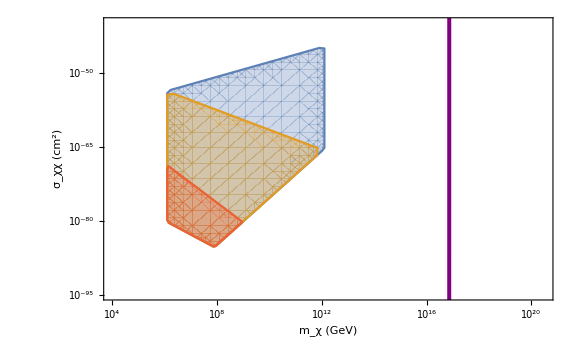

```mathematica
XLabelCollision={{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"},{10,"10^10"},{12,"10^12"},{14,"10^14"},{16,"10^16"},{18,"10^18"},{20,"10^20"},{22,"10^22"},{24,"10^24"},{26,"10^26"},{28,"10^28"},{30,"10^30"}};
YLabelCollision={{-110,"10^-110"},{-105,"10^-105"},{-100,"10^-100"},{-95,"10^-95"},{-90,"10^-90"},{-85,"10^-85"},{-80,"10^-80"},{-75,"10^-75"},{-70,"10^-70"},{-65,"10^-65"},{-60,"10^-60"},{-55,"10^-55"},{-50,"10^-50"},{-45,"10^-45"},{-40,"10^-40"},{-35,"10^-35"},{-30,"10^-30"},{-25,"10^-25"},{-20,"10^-20"},{-15,"10^-15"},{-10,"10^-10"},{-5,"10^-5"},{0,"1"}};
eboomlimitcollisionf1=Plot[(200 Sign[x-(eboom[1.25]-Log10[1])]),{x,15,25},ExclusionsStyle->Directive[{Thickness[.005],Purple}],PlotRange->{-120,10}];
canvascapture=Plot[-500,{logmdm,4,20.5},Frame->True,FrameTicks->{{YLabelCollision,None},{XLabelCollision,None}},LabelStyle-> {Directive[Bold],Medium},FrameStyle->Black,FrameLabel->{"m_χ (GeV)", "σ_χχ (cm^2)"},PlotRange->{-95,-40},Axes->None];
collapseplotfull=Show[canvascapture,multicollapse,Rχχcollapse,BHcollapse,Fermicollapse,eboomlimitcollisionf1,ImageSize->Large]
```

#### If you satisfy boom, everything else aight

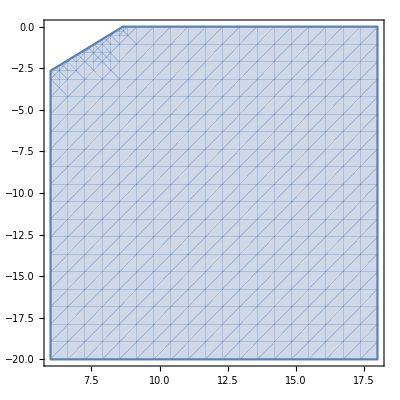

```mathematica
depletecloudt1=RegionPlot[((Γcap t1)/Rcloud^3)^2 10^logσ cm^2 vesc[1.25] Rcloud^3 (3 10^10 cm/s)^2(0.2 GeV 10^-13 cm)^-1 1/GeV<Γcap 1/GeV,{logmdm,6,18},{logσ,-20,0}]
```

```mathematica
Clear[logσχA];
infall1=(Γcap^2(10^logmdm GeV)^2 10^logσ cm^2)/(σχA^2(10^19 GeV)^4(10^-3.5)^4)(4000 10^5 cm)/vesc[1.25] 0.2GeV 10^-13 cm;
infall2=(Γcap^2(10^logmdm GeV)^2 10^logσ cm^2)/(σχA^2(10^19 GeV)^4(10^-3.5)^2 Rth^2)((4000 10^5 cm)^3)/vesc[1.25]^3 0.2GeV 10^-13 cm;
```

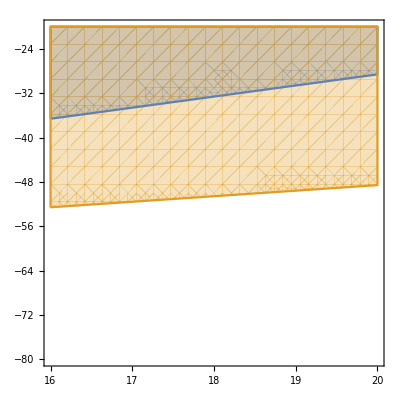

```mathematica
Clear[logσχA];
logσχA=-31;
RegionPlot[{infall1 10^17 s(GeV 10^-24 s)^-1>1,infall2 10^17 s(GeV 10^-24 s)^-1>1},{logmdm,16,20},{logσ,-80,-20}]
Clear[logσχA];
```

```mathematica
{t1,t2,Γcap (GeV 10^-24 s)^-1,Nsg/Γcap GeV 10^-24 s}/.{logmdm->16,logσχA->-35}//N
```

{2.23772×10^15 s,3.74612×10^13 s,3466.96/s,8.01711×10^8 s}

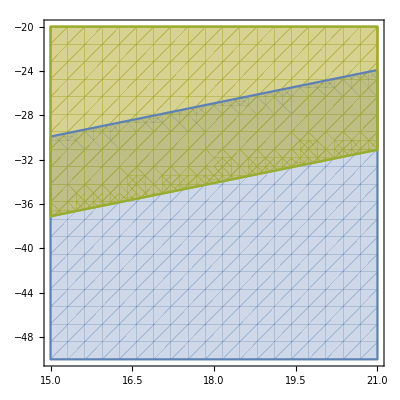

```mathematica
RegionPlot[{logσχA<Log10[xenonSI coherence/cm^2],(t1+t2)/s<10^17,t1/s<10^17},{logmdm,15,21},{logσχA,-50,-20}]
```

#### Over collection

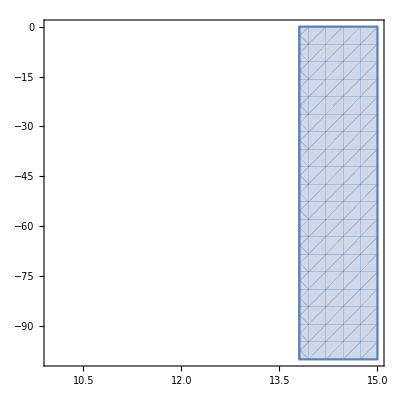

```mathematica
RegionPlot[Γcap (0.2 GeV 10^-13 cm)^-1(3 10^10 cm/s )tcol1 1/Ncrit>1,{logmdm,10,15},{logσ,0,-100}]
```

```mathematica
((10^31 cm^-3 10 GeV)/(0.4 GeV/cm^3))^(2/3)(10^-3/vesc[1.25])^2(10^-3.5)^(2/3)1/((4000 10^5 cm)^2)(10^-6 GeV ((10^19 GeV)^2)/(10^31 cm^-3 10 GeV))(0.2 GeV 10^-13 cm)^-1
```

1.03767×10^13 GeV

#### Single decay

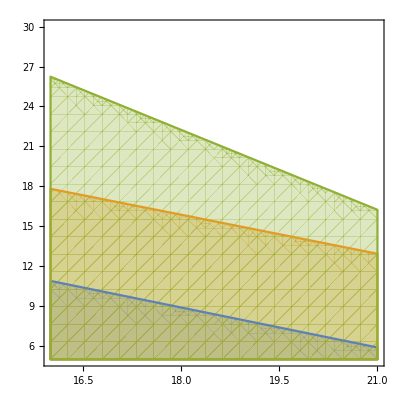

```mathematica
Clear[logσχA];
logσχA=-30;
RegionPlot[{Γtrans 0.1s (GeV 10^-24 s)^-1((5Gyr)/(10^logτχ Gyr))>1,Γcap t2 (GeV 10^-24 s)^-1((5Gyr)/(10^logτχ Gyr))>1,Γcap 10^17 s (GeV 10^-24 s)^-1((5Gyr)/(10^logτχ Gyr))>1},{logmdm,16,21},{logτχ,5,30}]
Clear[logσχA];
```

#### Multi decays - useless

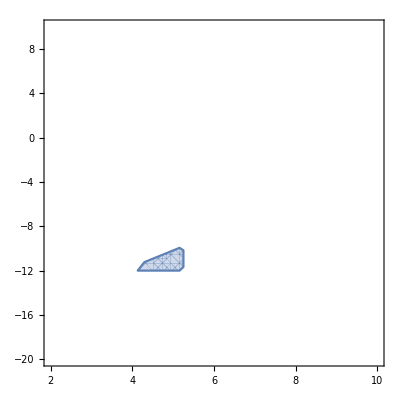

```mathematica
boomdecaylife=10^logmdm>10^eboom[1.25]/(Nlife Min[1,((triggermass[1.25] cm)/Rth)^3]((10^-12 s)/(10^logτχ s)));
RegionPlot[{Nlife<Nsg&&boomdecaylife&&((10^-12 s)/(10^logτχ s))<1},{logmdm,2,10},{logτχ,-20,10}]
```

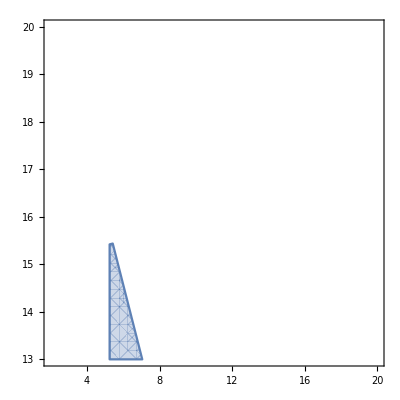

```mathematica
boomdecaycollapse=10^logmdm>10^eboom[1.25]/(Nsg  ((10^-12 s)/(10^logτχ s)));
RegionPlot[{Nsg<Nlife&&boomdecaycollapse&&(10^-12 s)/(10^logτχ s)<1},{logmdm,2,20},{logτχ,13,20}]
```

#### Wind vs. cloud constraints (decay or collision)

```mathematica
Rcloud=((10^logmdm GeV)/(10GeV))Rwd/Max[1,Nscat]/.{Rwd->4000 10^5 cm};
cloudnd=(Γcap τwd)/Rcloud^3(0.2GeV 10^-13 cm)^-1(3 10^10 cm/s)/.{Rwd->4000 10^5 cm,τwd->(5 10^9)π 10^7 s};
windnd=(Γtrans (Rwd/vesc[1.25]))/Rwd^3(0.2GeV 10^-13 cm)^-1/.{Rwd->4000 10^5 cm,τwd->(5 10^9)π 10^7 s};
```

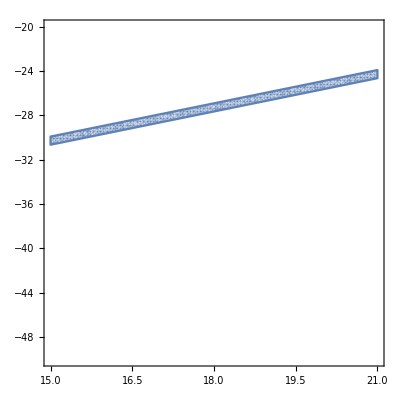

```mathematica
RegionPlot[{cloudnd cm^3>windnd cm^3&&logσχA<Log10[xenonSI coherence/cm^2]&&(t1+t2)/s<10^17},{logmdm,15,21},{logσχA,-50,-20},PlotPoints->50]
```

#### Testing

```mathematica
Simplify[ρwd^(2/5)/T^(3/5)(0.2GeV 10^-13 cm)^(6/5)/.{ρwd->10^14 g/cm^3(10^24 GeV)/g,T->10^-7 GeV},{cm>0,GeV>0}]
```

914.61 GeV

```mathematica
Becboom=Simplify[mdm ((ρcrit/mdm)^2 σ ((1/(G mdm^2 ρcrit))^(1/4)Sqrt[G ρcrit])(Min[4 10^-5,(1/(G mdm^2 ρcrit)(0.2GeV 10^-13 cm)^4)^(1/4)1/cm]cm)^3(10^-12 s))/.{ρcrit->(mdm^5 T^3)/ρwd}/.G->1/Mpl^2/.param,{cm>0,GeV>0}](0.2 GeV 10^-13 cm)^-6 3 10^10 cm/s;
```

```mathematica
Becbhboom=mdm^3 Mpl^4 σ 10^-12 s/.param
```

10^(64+3 logmdm+logσ) cm^2 GeV^7 s

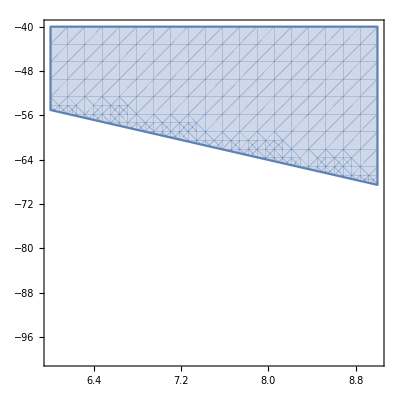

```mathematica
RegionPlot[{Becboom/GeV>10^eboom[1.25]},{logmdm,6,9},{logσ,-40,-100}]
```

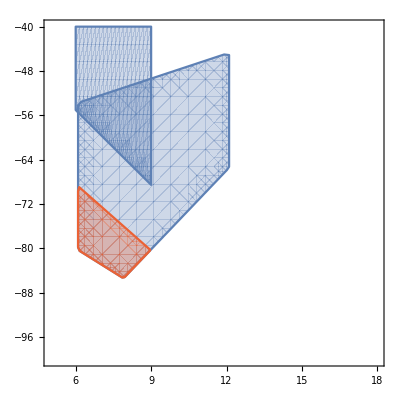

```mathematica
Show[multicollapse,Fermicollapse,-Graphics-]
```

```mathematica
Msgboson=Simplify[(T^3/(G^3 ρwd mdm))^(1/4)/.{G->1/((10^19 GeV)^2)}/.param,GeV>0]
```

1.66718×10^26 (10^-logmdm)^(1/4) GeV

```mathematica
Nchboson=(Mpl/mdm)^2/.param;
```

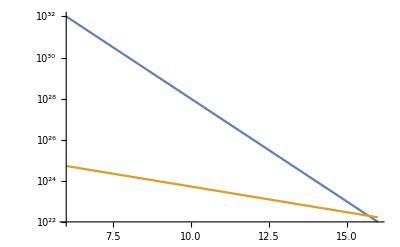

```mathematica
LogPlot[{Nchboson 10^logmdm,Msgboson/GeV},{logmdm,6,16}]
```

```mathematica
rbec=Simplify[(Mpl^2/(mdm^2 ρcrit))^(1/4)/.ρcrit->(mdm^5 T^3)/ρwd/.param,GeV>0]0.2GeV 10^-13 cm;
```

```mathematica
rbec/.logmdm->9
```

2.13327×10^-18 cm